## Graphene

## Bulk

```mathematica
Clear[bulkHam];
bulkHam[{kx_,ky_}]:=Module[{ham,t=1,r1,r2,k,dx,dy},
r1={Sqrt[3]/2,3/2};
r2={-Sqrt[3]/2,3/2};
k={kx,ky};
dx=t*(1+Cos[k.r1]+Cos[k.r2]);
dy=t*(Sin[k.r1]+Sin[k.r2]);
ham=dx*PauliMatrix[1]+dy*PauliMatrix[2];
Return[ham];
]
```

```mathematica
pathBZ[dd_]:=Module[{path,path1,path2,path3,b=4*π/3},
path1=Table[{b/2/Sqrt[3]*m/2,b/2*m/2},{m,0,2,dd}];
path2=Table[{b/(2*Sqrt[3])*(3-m),b/2},{m,2+dd,3,dd}];
path3=Table[{0,b/2*(3+Sqrt[3]-m)/Sqrt[3]},{m,3,3+Sqrt[3],dd}];
path=Join[path1,path2,path3];
Return[path];
]
```

```mathematica
el=Eigenvalues/@Map[bulkHam,pathBZ[1/10]];
```

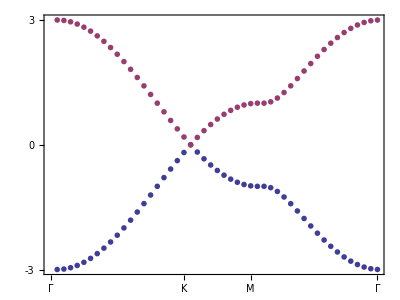

```mathematica
ListPlot[Transpose[el],Frame->True,PlotTheme->"Classic",
PlotStyle->PointSize[0.01],
Joined->False,AspectRatio->0.75,
FrameTicks->{{{-3,0,3},None},{{{0,"Γ"},{20,"K"},{30,"M"},{49,"Γ"}},None}},
FrameStyle->Directive[Gray,FontSize->15]
]
```

## Zig-zag edge

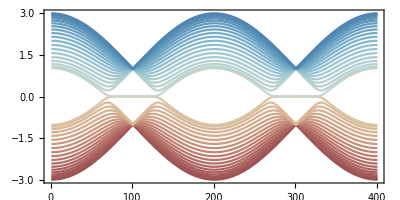

```mathematica
hamiltonian[kx_,num_]:=Module[{ham,hx,h00,h01,a=1},
h00=DiagonalMatrix[Table[m*(-1)^(i+1),{i,1,2*num}]]+DiagonalMatrix[Table[t,{i,1,2*num-1}],-1]+DiagonalMatrix[Table[t,{i,1,2*num-1}],1];
hx=DiagonalMatrix[{t*Exp[ⅈ*kx]},-1]+DiagonalMatrix[{t*Exp[-ⅈ*kx]},1];
h01=KroneckerProduct[DiagonalMatrix[Table[1,{i,1,num}]],hx];
ham=h00+h01;
Return[ham]
]
hk=hamiltonian[kx,20]//Normal;
el=ParallelTable[Sort@Eigenvalues[hk/.{kx->kk,t->1,m->0}],{kk,0,4*π,0.01*π}];
ListPlot[Transpose@Re@el,AspectRatio->0.5,Frame->True,PlotRange->All,Joined->True,ColorFunction->"RedBlueTones"]
```